## Metropolis Hastings

Bayesian Statistics


What is a Markov Chain?

What is MCMC? 

Metropolis Hastings

```mathematica
sampleWithMCMC[dist_,priordist_, steps_, xmin_, xmax_]:=(
calculatePosterior[x_]:=Likelihood[dist,{x}] * PDF[priordist, x];
moveToNextStep[old_, new_]:= If[RandomReal[] <=Min[1,calculatePosterior[new]/calculatePosterior[old]],new,old];
walk = FoldList[moveToNextStep,RandomVariate[priordist, steps]];
l=Plot[{PDF[dist,x],PDF[priordist,x]},{x,xmin,xmax}, PlotRange->{{xmin,xmax},All}, PlotStyle->{Darker[Green],Darker[Red]}, PlotLegends->Placed[{"Posterior Distribution", "Prior Distribution"},Above]];
sh=Histogram[walk,Automatic,"PDF", PlotRange->{{xmin,xmax},All}];
distplot=Show[sh,l];
trace=ListLinePlot[walk];
GraphicsGrid[{{distplot,trace}}, ImageSize->{600,Automatic}]
)
```

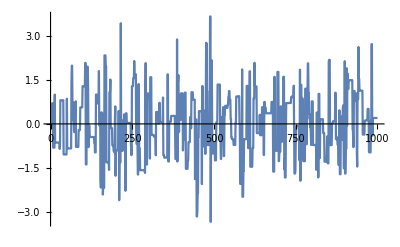

```mathematica
sampleWithMCMC[NormalDistribution[0,1], UniformDistribution[{-5,5}],10000,-5, 5]
```

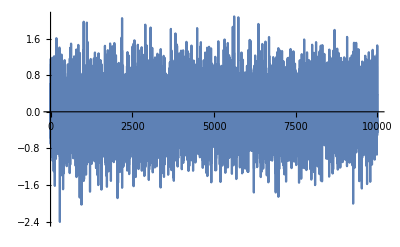

```mathematica
sampleWithMCMC[NormalDistribution[0,1], NormalDistribution[0,1],10000,-5, 10]
```

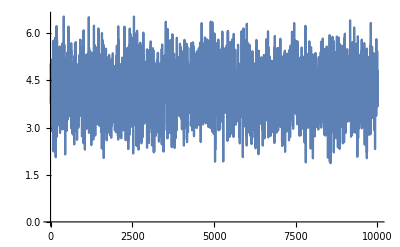

```mathematica
sampleWithMCMC[GammaDistribution[2,1/2],NormalDistribution[5,1],10000, 0,16]
```

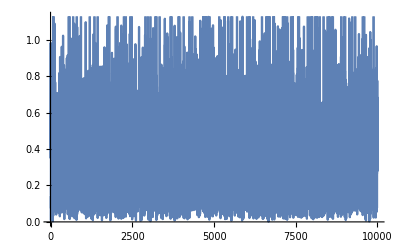

```mathematica
sampleWithMCMC[GammaDistribution[2,1/2], ExponentialDistribution[2],10000, 0,6]
```

```mathematica
(*Integrate[Log[x+2y+3z,E] Sin[x+y+z],{x,0,1},{y,0,1},{z,0,1}]*)
```

```mathematica
𝒹=MultinormalDistribution[{3,2},{{1,0.5},{0.5,1}}];
dist = 𝒹;
priordist = MultinormalDistribution[{-3,-2},{{1,0.5},{0.5,1}}];
Plot3D[{PDF[dist,{x,y} ],PDF[priordist,{x,y}]},{x,-10,10},{y,-10,10} ,PlotRange->{{-10,10},{-10,10},{0,0.2}}, Mesh->None]
burin=1000;
steps=1000;
calculatePosterior[x_]:=Likelihood[dist,{x}] * RandomVariate[priordist];
moveToNextStep[old_, new_]:= If[RandomReal[] <=Min[1,calculatePosterior[new]/calculatePosterior[old]],new,old];
walk=FoldList[moveToNextStep,RandomVariate[priordist, burin+steps]];
ListPlot3D[Transpose[{Table[Take[walk,-steps][[i,1]],{i,1, steps}],Table[Take[walk,-steps][[i,2]],{i,1, steps}], Table[calculatePosterior[i],{i,Take[walk,-steps]}]}]]
Histogram3D[walk,PlotRange->{{-10,10},{-10,10},Automatic}]
ListLinePlot[walk]
```